```mathematica
roundHalf[x_]:=
If[IntegerQ[x],Throw["Integer"],Floor[x]+1/2];
```

```mathematica
roundSet[x_,which_]:=
If[which==1,
Round[x-1/2,2]+1/2,
Round[x-3/2,2]+3/2];
```

```mathematica
inDomain[x_,which_,extended_:False]:=
If[IntegerQ[x],
If[Not[extended],Throw["Integer"],True],
Xor[Mod[Floor[x],2]==0,which==0]];
```

```mathematica
whichDomain[x_]:=
If[IntegerQ[x],Throw["Integer"],
1-Mod[Floor[x],2]];
```

```mathematica
EE[x_,θ_,λ_,which_:-1]:= 
Module[{r = If[which==-1, roundHalf[x], roundSet[x,which]]},
λ(x-r)+r+θ
];
```

```mathematica
trajectory[x_,θ_,λ_,whichFirst_,depth_]:=
Module[{X={x},T={whichFirst}},
If[Catch[
While[Length[X]<depth,
AppendTo[X,EE[Last[X],θ,λ,Last[T]]];
AppendTo[T,whichDomain[Last[X]]];
];
]=="Integer",AppendTo[T,-1]];
{X,T}
];
```

```mathematica
trajectoryVisualize[x_,whichFirst_,depth_]:=
Manipulate[
Module[{tt = trajectory[x,θ,λ,whichFirst,depth],plts,X,T},
X = tt⟦1⟧;
T=tt⟦2⟧;
plts =Table[
If[i<Length[X],
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Blue,AspectRatio->0.15],
If[i==Length[X],
If[i<depth,
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Red,AspectRatio->0.15],
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Blue,AspectRatio->0.15]],
NumberLinePlot[{}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},AspectRatio->0.15]]],
{i,1,depth}];
GraphicsColumn[plts]
],
{θ,0,2},
{{λ,2},1,2}];
```

```mathematica
trajectoryVisualizeThetaFunc[x_,whichFirst_,depth_,thetaFunc_]:=
Manipulate[
Module[{tt = trajectory[x,thetaFunc[λ],λ,whichFirst,depth],plts,X,T},
X = tt⟦1⟧;
T=tt⟦2⟧;
plts =Table[
If[i<Length[X],
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Blue,AspectRatio->0.15],
If[i==Length[X],
If[i<depth,
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Red,AspectRatio->0.15],
NumberLinePlot[{Mod[X⟦i⟧,2]}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},PlotStyle->Blue,AspectRatio->0.15]],
NumberLinePlot[{}, PlotRange->{{0,2},All},Ticks->{{0,1,2},Automatic},AspectRatio->0.15]]],
{i,1,depth}];
GraphicsColumn[plts]
],
{{λ,2},1,2}];
```

```mathematica
trajectoryVisualize[1,1,5]
```

```mathematica
f[l_]:=-1/2*(l^5-2*l^4-2*l^2-1)/(l^4+l^3+l^2+l+1);
```

```mathematica
trajectoryVisualizeThetaFunc[1,1,6,f]
```

```mathematica
dat = {{-1/2*{l^4-4*l^3-2*l^2-4*l-1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-2*l^3-2*l+1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-5}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-1}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^3-4*l^2-4*l-1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-4*l^3-3}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^4-2*l^3-2*l^2+1}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^3-2*l^2-2*l+1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-6*l^3-4*l^2-4*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-4*l^2-2*l-5}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-6*l^2-4*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^3-6*l^2-2*l-5}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-5}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-2*l^2-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-3}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-4*l^3-1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-2*l^3-2*l^2-2*l+1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^3-6*l^2-2*l-3}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^3-4*l^2-1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-3}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-4*l^3-2*l-1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^2-6*l-3}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^2-4*l-1}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-2*l^2-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^2-2*l-1}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^3-2*l^2-2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-2*l^2-2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*l+3/2,1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-2*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^2-4*l-3}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-4*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*l+5/2,1.00000000000000,2}};
```

```mathematica
r = ReflectionTransform[{-1,1}];
```

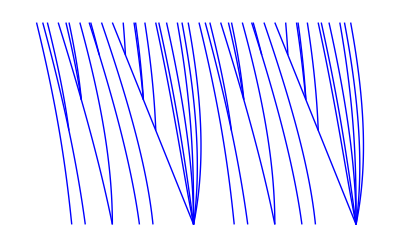

```mathematica
Show[
(Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat)/.L_Line:>{Blue,GeometricTransformation[L,r]},
PlotRange->All,
Axes->False]
```

```mathematica
dat2 = {{1/2*{l^4+4*l^2+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+4*l+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+4*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+2*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^4-2*l^3+2*l^2-1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3-2*l^2+2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4-2*l^3+2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3-2*l^2+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4-2*l^3+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l^2+2*l+5}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l^3+2*l^2+4*l+5}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4+4*l^2+4*l+1}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^3+3}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l+3}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4-2*l^3+2*l^2+2*l-1}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4+2*l^3+2*l^2+2*l+5}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4+4*l^2+4*l+3}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4+3}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4-2*l^3+2*l^2+2*l+1}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^3+4*l+3}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^3-2*l^2+2*l+1}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l^3+4*l^2+2*l+5}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+4*l^2+2*l+3}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+2*l^2+3}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4-2*l^3+2*l^2+1}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+2*l^3+2*l^2+4*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^2+3}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^4+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^2-2*l+1}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*l-1/2,1.00000000000000,2},{1/2*{l^4+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^2+1}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^3+2*l+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*l+1/2,1.00000000000000,2},{1/2*{l^4+2*l^3+2*l^2+2*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l^2+2*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^2+2*l+3}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^3+2*l^2+4*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^3+4*l^2+4*l+3}*{l-1}/{l^4-1},1.00000000000000,2}};
```

```mathematica
r = ReflectionTransform[{-1,1}];
```

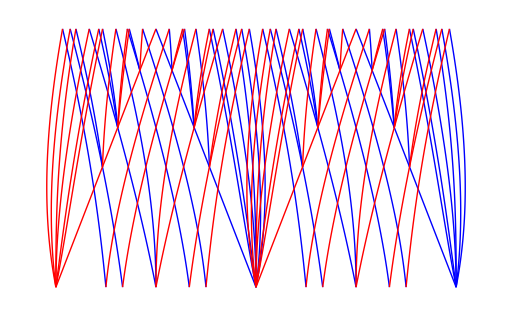

```mathematica
t = {Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat,
Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat2};
Show[t⟦1⟧/.L_Line:>{Blue,GeometricTransformation[L,r]},t⟦2⟧/.L_Line :> {Red, GeometricTransformation[L,r]},
PlotRange->All,
Axes->False]
```

```mathematica
Solve[x^2-x-1==0,x]//N
```

{{x→-0.618034},{x→1.61803}}

```mathematica
(1/18*Sqrt[31]*Sqrt[3]+29/54)^(1/3)+1/9/(1/18*Sqrt[31]*Sqrt[3]+29/54)^(1/3)+1/3//FullSimplify
```

Root[-1-#1^2+#1^3&,1]

```mathematica
Reduce[-1/2*(l^5-2*l^4-2*l^2+2*l-1)*(l-1)/(l^5-1)
==-1/2*(l^6-2*l^5-2*l^3+2*l^2-2*l+1)*(l-1)/(l^6-1)]//N
```

l==1.4036||l==-0.656781-0.837593 ⅈ||l==-0.656781+0.837593 ⅈ||l==0.45498-0.649504 ⅈ||l==0.45498+0.649504 ⅈ

```mathematica
dat = {{-1/2*{l^5-2*l^4-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^4-2*l^3-1}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-2*l^4-2*l+1}/{l^4+l^3+l^2+l+1},1.38027756909760,2},{-1/2*{l^3-2*l^2-1}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-2*l^4-2*l^2+2*l-1}/{l^4+l^3+l^2+l+1},1.83928675521417,2},{-1/2*{l^4-2*l^3-2*l+1}/{l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^5-2*l^4-2*l^2+1}/{l^4+l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^5-2*l^4-2*l^2-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^2-2*l-1}/{l+1},1.00000000000000,2},{-1/2*{l^5-2*l^4-2*l^3+2*l^2-2*l+1}/{l^4+l^3+l^2+l+1},1.92756197548292,2},{-1/2*{l^5-2*l^4-2*l^3+2*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.61803398874990,2},{-1/2*{l^3-2*l^2-2*l+1}/{l^2+l+1},1.61803398875005,2},{-1/2*{l^4-2*l^3-2*l^2+1}/{l^3+l^2+l+1},1.61803398874989,2},{-1/2*{l^5-2*l^4-2*l^3+1}/{l^4+l^3+l^2+l+1},1.61803398874990,2},{-1/2*{l^5-2*l^4-2*l^3-1}/{l^4+l^3+l^2+l+1},1.32471795724475,2},{-1/2*{l^4-2*l^3-2*l^2-1}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-2*l^4-2*l^3-2*l+1}/{l^4+l^3+l^2+l+1},1.75487766624669,2},{-1/2*{l^5-2*l^4-2*l^3-2*l-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-2*l^2-2*l-1}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^4-2*l^3-2*l^2-2*l+1}/{l^3+l^2+l+1},1.83928675521426,2},{-1/2*{l^5-2*l^4-2*l^3-2*l^2+1}/{l^4+l^3+l^2+l+1},1.83928675521401,2},{-1/2*{l^5-2*l^4-2*l^3-2*l^2-1}/{l^4+l^3+l^2+l+1},1.32471795724475,2},{-1/2*{l^4-2*l^3-2*l^2-2*l-1}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-2*l^4-2*l^3-2*l^2-2*l+1}/{l^4+l^3+l^2+l+1},1.92756197548293,2},{-1/2*{l^5-2*l^4-2*l^3-2*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*l+3/2,1.00000000000000,2},{-1/2*{l^5-4*l^4-1}/{l^4+l^3+l^2+l+1},1.92756197548293,2},{-1/2*{l^5-4*l^4-3}/{l^4+l^3+l^2+l+1},1.83928675521416,2},{-1/2*{l^4-4*l^3-1}/{l^3+l^2+l+1},1.83928675521416,2},{-1/2*{l^5-4*l^4-2*l-1}/{l^4+l^3+l^2+l+1},1.75487766624669,2},{-1/2*{l^5-4*l^4-2*l-3}/{l^4+l^3+l^2+l+1},1.61803398875002,2},{-1/2*{l^4-4*l^3-3}/{l^3+l^2+l+1},1.61803398874989,2},{-1/2*{l^3-4*l^2-1}/{l^2+l+1},1.61803398874989,2},{-1/2*{l^5-4*l^4-2*l^2-1}/{l^4+l^3+l^2+l+1},1.61803398874974,2},{-1/2*{l^5-4*l^4-2*l^2-3}/{l^4+l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^4-4*l^3-2*l-1}/{l^3+l^2+l+1},1.46557123187674,2},{-1/2*{l^5-4*l^4-2*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.38027756909761,2},{-1/2*{l^5-4*l^4-2*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l-3}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-4*l^2-3}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-4*l^2-1}/{l^4+l^3+l^2+l+1},1.92756197548307,2},{-1/2*{l^5-4*l^4-4*l^2-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^2-4*l-1}/{l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-2*l-1}/{l^4+l^3+l^2+l+1},1.83928675521399,2},{-1/2*{l^5-4*l^4-2*l^3-2*l-3}/{l^4+l^3+l^2+l+1},1.32471795724475,2},{-1/2*{l^4-4*l^3-2*l^2-3}/{l^3+l^2+l+1},1.00000002000000,2},{-1/2*{l^5-4*l^4-2*l^3-4*l-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-4*l^2-2*l-1}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-2*l^2-3}/{l^4+l^3+l^2+l+1},1.32471795724475,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-1}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-2*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-2*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-3}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-2*l^2-4*l-1}/{l^4+l^3+l^2+l+1},1.38027756909760,2},{-1/2*{l^3-4*l^2-2*l-3}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-2*l^3-4*l^2-3}/{l^4+l^3+l^2+l+1},1.83928675521417,2},{-1/2*{l^4-4*l^3-2*l^2-4*l-1}/{l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^5-4*l^4-2*l^3-4*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^5-4*l^4-2*l^3-4*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^2-4*l-3}/{l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-4*l^3-4*l-1}/{l^4+l^3+l^2+l+1},1.92756197548292,2},{-1/2*{l^5-4*l^4-4*l^3-4*l-3}/{l^4+l^3+l^2+l+1},1.61803398874989,2},{-1/2*{l^3-4*l^2-4*l-1}/{l^2+l+1},1.61803398875004,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-1}/{l^3+l^2+l+1},1.61803398874990,2},{-1/2*{l^5-4*l^4-4*l^3-2*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.61803398874989,2},{-1/2*{l^5-4*l^4-4*l^3-2*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.32471795724474,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-3}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-4*l^3-2*l^2-4*l-1}/{l^4+l^3+l^2+l+1},1.75487766624669,2},{-1/2*{l^5-4*l^4-4*l^3-2*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-4*l^2-4*l-3}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-1}/{l^3+l^2+l+1},1.83928675521426,2},{-1/2*{l^5-4*l^4-4*l^3-4*l^2-2*l-1}/{l^4+l^3+l^2+l+1},1.83928675521401,2},{-1/2*{l^5-4*l^4-4*l^3-4*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.32471795724475,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-3}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-4*l^4-4*l^3-4*l^2-4*l-1}/{l^4+l^3+l^2+l+1},1.92756197548293,2},{-1/2*{l^5-4*l^4-4*l^3-4*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*l+5/2,1.00000000000000,2},{-1/2*{l^5-6*l^4-2*l^3-2*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.92756197548292,2},{-1/2*{l^5-6*l^4-2*l^3-2*l^2-2*l-5}/{l^4+l^3+l^2+l+1},1.83928675521416,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-3}/{l^3+l^2+l+1},1.83928675521416,2},{-1/2*{l^5-6*l^4-2*l^3-2*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.75487766624669,2},{-1/2*{l^5-6*l^4-2*l^3-2*l^2-4*l-5}/{l^4+l^3+l^2+l+1},1.61803398875002,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-5}/{l^3+l^2+l+1},1.61803398874989,2},{-1/2*{l^3-6*l^2-2*l-3}/{l^2+l+1},1.61803398874989,2},{-1/2*{l^5-6*l^4-2*l^3-4*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.61803398874974,2},{-1/2*{l^5-6*l^4-2*l^3-4*l^2-2*l-5}/{l^4+l^3+l^2+l+1},1.46557123187677,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-3}/{l^3+l^2+l+1},1.46557123187674,2},{-1/2*{l^5-6*l^4-2*l^3-4*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.38027756909761,2},{-1/2*{l^5-6*l^4-2*l^3-4*l^2-4*l-5}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-5}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-6*l^2-2*l-5}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-6*l^4-2*l^3-6*l^2-2*l-3}/{l^4+l^3+l^2+l+1},1.92756197548307,2},{-1/2*{l^5-6*l^4-2*l^3-6*l^2-2*l-5}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^2-6*l-3}/{l+1},1.00000000000000,2},{-1/2*{l^5-6*l^4-4*l^3-2*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.83928675521399,2},{-1/2*{l^5-6*l^4-4*l^3-2*l^2-4*l-5}/{l^4+l^3+l^2+l+1},1.32471795724474,2},{-1/2*{l^4-6*l^3-4*l^2-2*l-5}/{l^3+l^2+l+1},1.00000002000000,2},{-1/2*{l^5-6*l^4-4*l^3-2*l^2-6*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^3-6*l^2-4*l-3}/{l^2+l+1},1.00000000000000,2},{-1/2*{l^5-6*l^4-4*l^3-4*l^2-2*l-5}/{l^4+l^3+l^2+l+1},1.32471795724473,2},{-1/2*{l^4-6*l^3-4*l^2-4*l-3}/{l^3+l^2+l+1},1.00000000000000,2},{-1/2*{l^5-6*l^4-4*l^3-4*l^2-4*l-3}/{l^4+l^3+l^2+l+1},1.00000000000000,2}};
```

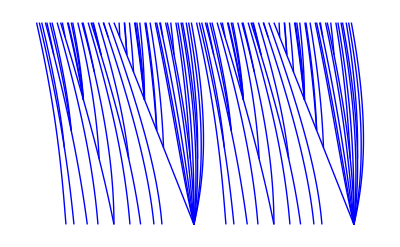

```mathematica
Show[
(Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat)/.L_Line:>{Blue,GeometricTransformation[L,ReflectionTransform[{-1,1}]]},
PlotRange->All,
Axes->False]
```